```mathematica
(*Cuerda 1, amarilla*)
```

```mathematica
(*m=2kg*)
```

```mathematica
datafrecond1={{1/1.68,12.4},{1/0.84,25.2},{1/0.56,36.5},{1/0.42,46.3},{1/0.336,57.1},{1/0.28,73.2},{1/0.24,86.1},{1/0.21,101.9}};
```

```mathematica
(*a es 1/lambda*)
```

```mathematica
datafit1=NonlinearModelFit[datafrecond1,{v*a+b},{v,b},a]
```

FittedModel[-1.51429+21.038 a]

```mathematica
datafit1[{"BestFit","ParameterTable"}]
```

{-1.51429+21.038 a, | Estimate | Standard Error | t-Statistic | P-Value
v | 21.038 | 0.641362 | 32.8021 | 5.34019×10^-8
b | -1.51429 | 1.92781 | -0.785496 | 0.462045}

```mathematica
(*m=1.5kg*)
```

```mathematica
datafrecond5={{1/1.68,11.3},{1/0.84,20.8},{1/0.56,28.7}};
```

```mathematica
datafit5=NonlinearModelFit[datafrecond5,{v*a+b},{v,b},a]
```

FittedModel[2.86667+14.616 a]

```mathematica
datafit5[{"BestFit","ParameterTable"}]
```

{2.86667+14.616 a, | Estimate | Standard Error | t-Statistic | P-Value
v | 14.616 | 0.775959 | 18.8361 | 0.0337662
b | 2.86667 | 0.997775 | 2.87306 | 0.213234}

```mathematica
(*Cuerda 2, roja*)
```

```mathematica
(*m=1kg*)
```

```mathematica
datafrecond2={{1/1.68,8.2},{1/0.84,17.2},{1/0.56,25.5},{1/0.42,35.5},{1/0.336,42.5},{1/0.28,54.1}};
```

```mathematica
datafit2=NonlinearModelFit[datafrecond2,{v*a+b},{v,b},a]
```

FittedModel[-1.04+15.1392 a]

```mathematica
datafit2[{"BestFit","ParameterTable"}]
```

{-1.04+15.1392 a, | Estimate | Standard Error | t-Statistic | P-Value
v | 15.1392 | 0.403486 | 37.521 | 3.01299×10^-6
b | -1.04 | 0.935328 | -1.11191 | 0.328499}

```mathematica
(*m=1.5kg*)
```

```mathematica
datafrecond3={{1/1.68,10.5},{1/0.84,21},{1/0.56,30.8},{1/0.42,42.1},{1/0.336,51.7},{1/0.28,62.9}};
```

```mathematica
datafit3=NonlinearModelFit[datafrecond3,{v*a+b},{v,b},a]
```

FittedModel[-0.04+17.5392 a]

```mathematica
datafit3[{"BestFit","ParameterTable"}]
```

{-0.04+17.5392 a, | Estimate | Standard Error | t-Statistic | P-Value
v | 17.5392 | 0.169434 | 103.516 | 5.22207×10^-8
b | -0.04 | 0.392768 | -0.101841 | 0.923784}

```mathematica
(*m=2kg*)
```

```mathematica
datafrecond4={{1/1.68,11.8},{1/0.84,24},{1/0.56,34.6},{1/0.42,48.9},{1/0.336,60.4},{1/0.28,72.5}};
```

```mathematica
datafit4=NonlinearModelFit[datafrecond4,{v*a+b},{v,b},a]
```

FittedModel[-0.666667+20.496 a]

```mathematica
datafit4[{"BestFit","ParameterTable"}]
```

{-0.666667+20.496 a, | Estimate | Standard Error | t-Statistic | P-Value
v | 20.496 | 0.318336 | 64.3849 | 3.48592×10^-7
b | -0.666667 | 0.73794 | -0.903416 | 0.417393}

```mathematica
(*Gráficas*)
```

```mathematica
graph1=Plot[datafit1[a],{a,0,5},PlotLegends->{"Cuerda 1, 2 kg"},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{0.2,5},{5,105}},Frame->True,FrameLabel->{Style["λ⁻.b9 / m⁻.b9",Bold,16],Style["𝜈 / Hz",16,Bold]}];
```

```mathematica
pplot1=ListPlot[datafrecond1 ,PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
(*dataerr1=ErrorListPlot[{{{1/1.68,12.4},ErrorBar[0.00708,0.1]},{{1/0.84,25.2},ErrorBar[0.014,0.1]},{{1/0.56,36.5},ErrorBar[0.0212,0.1]},{{1/0.42,46.3},ErrorBar[0.0283,0.1]},{{1/0.336,57.1},ErrorBar[0.035,0.1]},{{1/0.28,73.2},ErrorBar[0.0425,0.1]},{{1/0.24,86.1},ErrorBar[0.0496,0.1]},{{1/0.21,101.9},ErrorBar[0.0566,0.1]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];*)
```

```mathematica
dataerr1=ErrorListPlot[{{{1/0.28,73.2},ErrorBar[0.0425,0.1]},{{1/0.24,86.1},ErrorBar[0.0496,0.1]},{{1/0.21,101.9},ErrorBar[0.0566,0.1]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
graph5=Plot[datafit5[a],{a,0,5},PlotLegends->{"Cuerda 1, 1.5 kg"},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Red,White}],Thick},PlotRange->{{0,5},{0,105}},Frame->True,FrameLabel->{Style["λ⁻.b9 / m⁻.b9",Bold,16],Style["𝜈 / Hz",16,Bold]}];
```

```mathematica
pplot5=ListPlot[datafrecond5 ,PlotLegends -> {"Datos experimentales"},PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
(*Los errores en la cuerda 1, 1.5 kg, no se aprecian*)
```

```mathematica
(*dataerr5=ErrorListPlot[{{{1/1.68,11.3},ErrorBar[0.00708,0.1]},{{1/0.84,20.8},ErrorBar[0.014,0.1]},{{1/0.56,28.7},ErrorBar[0.0212,0.1]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];*)
```

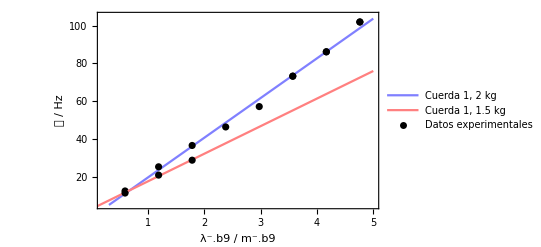

```mathematica
Show[graph1,pplot1,dataerr1,graph5,pplot5]
```

```mathematica
graph2=Plot[datafit2[a],{a,0,5},PlotLegends->{"Cuerda 2, 1 kg"},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Red,White}],Thick},PlotRange->{{0.2,4},{5,80}},Frame->True,FrameLabel->{Style["λ⁻.b9 / m⁻.b9",Bold,16],Style["𝜈 / Hz",16,Bold]}];
```

```mathematica
pplot2=ListPlot[datafrecond2,PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
dataerr2=ErrorListPlot[{{{1/0.42,35.5},ErrorBar[0.0283,0.1]},{{1/0.336,42.5},ErrorBar[0.0354,0.1]},{{1/0.28,54.1},ErrorBar[0.0425,0.1]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
graph3=Plot[datafit3[a],{a,0,5},PlotLegends->{"Cuerda 2, 1.5 kg"},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{0.2,5},{5,105}},Frame->True,FrameLabel->{Style["λ⁻.b9 / m⁻.b9",Bold,16],Style["𝜈 / Hz",16,Bold]}];
```

```mathematica
pplot3=ListPlot[datafrecond3 ,PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
dataerr3=ErrorListPlot[{{{1/0.42,42.1},ErrorBar[0.0283,0.1]},{{1/0.336,51.7},ErrorBar[0.0354,0.1]},{{1/0.28,62.9},ErrorBar[0.0425,0.1]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
graph4=Plot[datafit4[a],{a,0,5},PlotLegends->{"Cuerda 2, 2 kg"},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Black,White}],Thick},PlotRange->{{0.2,5},{5,105}},Frame->True,FrameLabel->{Style["λ⁻.b9 / m⁻.b9",Bold,16],Style["𝜈 / Hz",16,Bold]}];
```

```mathematica
pplot4=ListPlot[datafrecond4 ,PlotLegends -> {"Datos experimentales"},PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
dataerr4=ErrorListPlot[{{{1/0.42,48.9},ErrorBar[0.0283,0.1]},{{1/0.336,60.4},ErrorBar[0.0354,0.1]},{{1/0.28,72.5},ErrorBar[0.0425,0.1]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

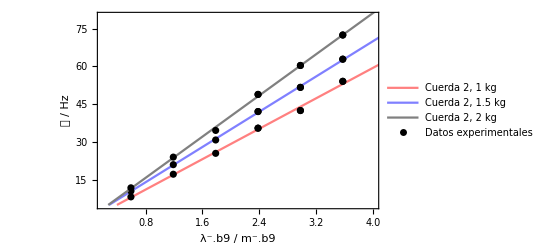

```mathematica
Show[graph2,pplot2,dataerr2,graph3,pplot3,dataerr3,graph4,pplot4,dataerr4]
```

```mathematica
(*Cálculo de las sigmas y rhos, densidades*)
```

```mathematica
σ[τ_,v_]:=τ/v^2;
```

```mathematica
ϵσ[τ_,v_,ϵv_]:=(2*τ/v^3)*ϵv;
```

```mathematica
σ[{14.7,19.6,9.8,14.7,19.6},{14.616,21.038,15.1392,17.5392,20.496}]
```

{0.0688114,0.044284,0.0427583,0.0477857,0.0466571}

```mathematica
ϵσ[{14.7,19.6,9.8,14.7,19.6},{14.616,21.038,15.1392,17.5392,20.496},{0.7759,0.64136,0.403,0.1694,0.318}]
```

{0.00730579,0.00270007,0.00227642,0.000923063,0.00144779}

```mathematica
ρ[σ_,R_]:=σ/(Pi*R^2);
```

```mathematica
ϵρ[R_,σ_,ϵR_,ϵσ_]:=Sqrt[(ϵσ/(Pi*R^2))^2+(((2*σ)/(Pi*R^3))*ϵR)^2];
```

```mathematica
ρ[{0.06881137975073766,0.044284033416153216,0.04275827961134217,0.047785680382456695,0.046657111290274424},{0.00115,0.00115,0.001,0.001,0.001}]
```

{16562.1,10658.6,13610.4,15210.7,14851.4}

```mathematica
ϵρ[{0.00115,0.00115,0.001,0.001,0.001},{0.06881137975073766,0.044284033416153216,0.04275827961134217,0.047785680382456695,0.046657111290274424},{0.000025,0.000025,0.000025,0.000025,0.000025},{0.007305794957388801,0.0027000672755760078,0.002276419716150245,0.0009230631108360886,0.001447790924112731}]
```

{1900.15,798.181,994.063,815.316,873.951}

```mathematica
(*Cálculo de frec 1 teórica*)
```

```mathematica
f1[v_,λ1_]:=v/λ1;
```

```mathematica
f1[{14.616,21.038,15.1392,17.5392,20.496},{1.68,1.68,1.68,1.68,1.68}]
```

{8.7,12.5226,9.01143,10.44,12.2}

```mathematica
ϵf1[v_,λ1_,ϵv_,ϵλ1_]:=Sqrt[(ϵv/λ1)^2+((v/λ1^2)*ϵλ1)^2]
```

```mathematica
ϵf1[{14.616,21.038,15.1392,17.5392,20.496},{1.68,1.68,1.68,1.68,1.68},{0.776,0.641,0.4,0.17,0.318},{0.02,0.02,0.02,0.02,0.02}]
```

{0.473374,0.409638,0.261148,0.16027,0.238586}

```mathematica
(*densidades medias*)
```

```mathematica
σmed1=(68.811379+44.28403)/2
```

56.5477

```mathematica
ϵσmed1=Sqrt[(1/2)*((68.811379-56.5477045)^2+(44.28403-56.5477045)^2)]
```

12.2637

```mathematica
σmed2=(42.75827961134217+47.785680382456695+46.657111290274424)/3
```

45.7337

```mathematica
ϵσmed2=Sqrt[(1/(3*2))*((45.73369042802443-42.75827961134217)^2+(45.73369042802443-47.785680382456695)^2+(45.73369042802443-46.657111290274424)^2)]
```

1.52296

```mathematica
ρmed1=(16.562073691196147+10.658635641931882)/2
```

13.6104

```mathematica
ϵρmed1=Sqrt[(1/2)*((13.610354666564014-16.562073691196147)^2+(13.610354666564014-10.658635641931882)^2)]
```

2.95172

```mathematica
ρmed2=(13.610383116501023+15.21065448375479+14.851419784471707)/3
```

14.5575

```mathematica
ϵρmed2=Sqrt[(1/6)*((14.557485794909173-13.610383116501023)^2+(14.557485794909173-15.21065448375479)^2+(14.557485794909173-14.851419784471707)^2)]
```

0.484773